```mathematica
m=500;
P1=RandomReal[{-1,1},m];
U1=RandomInteger[{0,1},m];
Q1=Table[(2U1[[k]]-1)*Sqrt[1-P1[[k]]^2],{k,m}];
R1=Table[0,{i,0,m}];
S1=Table[0,{i,0,m}];
P2=RandomReal[{-1,1},m];
U2=RandomInteger[{0,1},m];
Q2=Table[(2U2[[k]]-1)*Sqrt[1-P2[[k]]^2],{k,m}];
R2=Table[0,{i,0,m}];
S2=Table[0,{i,0,m}];
P3=RandomReal[{-1,1},m];
U3=RandomInteger[{0,1},m];
Q3=Table[(2U3[[k]]-1)*Sqrt[1-P3[[k]]^2],{k,m}];
R3=Table[0,{i,0,m}];
S3=Table[0,{i,0,m}];
P4=RandomReal[{-1,1},m];
U4=RandomInteger[{0,1},m];
Q4=Table[(2U4[[k]]-1)*Sqrt[1-P4[[k]]^2],{k,m}];
R4=Table[0,{i,0,m}];
S4=Table[0,{i,0,m}];
P5=RandomReal[{-1,1},m];
U5=RandomInteger[{0,1},m];
Q5=Table[(2U5[[k]]-1)*Sqrt[1-P5[[k]]^2],{k,m}];
R5=Table[0,{i,0,m}];
S5=Table[0,{i,0,m}];
For[k=1,k≤m,k+=1,{R1[[k+1]]=R1[[k]]+P1[[k]];S1[[k+1]]=S1[[k]]+Q1[[k]];R2[[k+1]]=R2[[k]]+P2[[k]];S2[[k+1]]=S2[[k]]+Q2[[k]];R3[[k+1]]=R3[[k]]+P3[[k]];S3[[k+1]]=S3[[k]]+Q3[[k]];R4[[k+1]]=R4[[k]]+P4[[k]];S4[[k+1]]=S4[[k]]+Q4[[k]];R5[[k+1]]=R5[[k]]+P5[[k]];S5[[k+1]]=S5[[k]]+Q5[[k]]}]
T1=Table[{R1[[j]],S1[[j]]},{j,1,m}];
T2=Table[{R2[[j]],S2[[j]]},{j,1,m}];
T3=Table[{R3[[j]],S3[[j]]},{j,1,m}];
T4=Table[{R4[[j]],S4[[j]]},{j,1,m}];
T5=Table[{R5[[j]],S5[[j]]},{j,1,m}];

p1=ListLinePlot[T1,Mesh->Full,ColorFunction->Function[{x,y},Hue[1]],MeshStyle->Red];
p2=ListLinePlot[T2,Mesh->Full,ColorFunction->Function[{x,y},Hue[0.6]],MeshStyle->Blue];
p3=ListLinePlot[T3,Mesh->Full,ColorFunction->Function[{x,y},Hue[0.3]],MeshStyle->Green];
p4=ListLinePlot[T4,Mesh->Full,ColorFunction->Function[{x,y},Hue[0.1]],MeshStyle->Orange];
p5=ListLinePlot[T5,Mesh->Full,ColorFunction->Function[{x,y},Hue[0.8]],MeshStyle->Purple];
Show[p1,p2,p3,p4,p5,PlotRange->All]
```

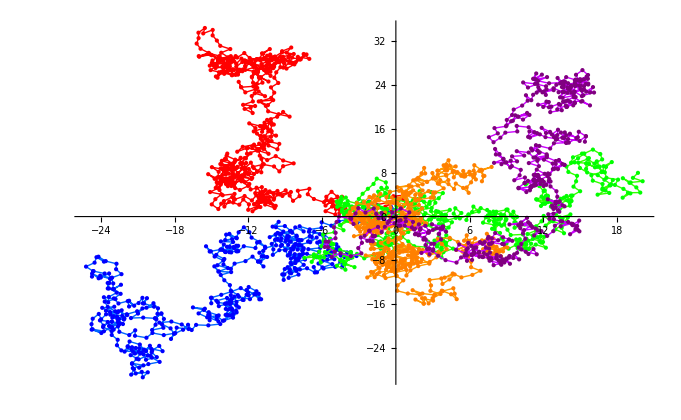

```mathematica
m=500;n=30;L1=1;L2=0.5;
V1=Array[0,{n,m}];
V2=Array[0,{n,m}];
For[l=1,l≤n,l+=1,
{P1=RandomReal[{-1,1},m];
U1=RandomInteger[{0,1},m];
Q1=Table[(2U1[[k]]-1)*Sqrt[1-P1[[k]]^2],{k,m}];
R1=Table[0,{i,0,m}];
S1=Table[0,{i,0,m}];
For[k=1,k≤m,k+=1,
  {R1[[k+1]]=R1[[k]]+L*P1[[k]];S1[[k+1]]=S1[[k]]+L1*Q1[[k]];
  V1[[l,k]]=R1[[k+1]]^2+S1[[k+1]]^2}]
}]
For[l=1,l≤n,l+=1,
{P2=RandomReal[{-1,1},m];
U2=RandomInteger[{0,1},m];
Q2=Table[(2U2[[k]]-1)*Sqrt[1-P2[[k]]^2],{k,m}];
R2=Table[0,{i,0,m}];
S2=Table[0,{i,0,m}];
For[k=1,k≤m,k+=1,
  {R2[[k+1]]=R2[[k]]+L*P2[[k]];S2[[k+1]]=S2[[k]]+L2*Q2[[k]];
  V2[[l,k]]=R2[[k+1]]^2+S2[[k+1]]^2}]
}]
Ave1=Table[Sum[V1[[i,j]]/n,{i,1,n}],{j,1,m}];
Ave2=Table[Sum[V2[[i,j]]/n,{i,1,n}],{j,1,m}];
pp1=ListLinePlot[Ave1,Mesh->Full,ColorFunction->Function[{x,y},Hue[0.1]],MeshStyle->Orange];
pp2=ListLinePlot[Ave2,Mesh->Full,ColorFunction->Function[{x,y},Hue[0.3]],MeshStyle->Green];
Show[pp1,pp2,PlotRange->All]
```